## 1 Venn diagrams

```mathematica
SetDirectory[NotebookDirectory[]];  (* makes it so any files exported will be saved in the same folder that this file is located in *)
```

### 1.1 Data Import, Initialization

```mathematica
data=Import["C:\\Users\\riiwi\\OneDrive - University of Maine System\\Will\\Data Collection and Analysis\\Surveys F21+F22\\F21+F22 Spins\\F21+F22SpinsNetworkReady.xlsx"][[1]];

data[[1]]
(* gets rid of the first row in the data table, which contains the names of the concepts associated with each column *)
data=Rest[data];

Dimensions[data]

(* this block removes the un/overconnected students from the data pool *)
overUnConnected={{171},{178},{183},{221},{232},{246},{247},{261}};
data=Delete[data,overUnConnected];
Export["F21+F22SpinsNetworkReady.1.xlsx",data];

Dimensions[data]

nStu=Dimensions[data][[1]];
nExp=20;
nConc=Dimensions[data][[2]];


For[i=1,i<=Dimensions[data][[1]],i++,
For[j=1,j<=Dimensions[data][[2]],j++,

(* splits the initial entries in the data table from single strings (a la "a,b,d,f") to a list of strings ( a la {"a","b","d","f"}) *)
data[[i,j]]=StringSplit[data[[i,j]],","];

(* converts the individual letters into their alphabetic numbers (a la "a"->1, "d"->4) *)
For[k=1,k<=Length@data[[i,j]],k++,
data[[i,j,k]]=LetterNumber[data[[i,j,k]]]
]
]
]


(* initializes the 4D array within which we will store the individual adjacency matrices for each student's answers for each concept *)
 vennArray=Table[0,nStu,nConc,nExp,nExp];

nStu
```

{Vector,Quantum State,Inner Product,Dot Product,Unit Vector,Basis Vector,Wave Function,Eigenvector,Eigenstate,Probability Amplitude,Probability}

{273,11}

{265,11}

265

### 1.2 Making the adjacency matrices

```mathematica
(* initializes the 4D array within which we will store the individual adjacency matrices for each student's answers for each concept *)
 vennArray=Table[0,nStu,nConc,nExp,nExp];

vennArray[[1,1]]//MatrixForm;

data//MatrixForm;

Dimensions[vennArray[[1,1]]];

For[i=1,i<=nStu,i++,
For[j=1,j<=nConc,j++,

(* this goes through each student's responses to each concept question (which expressions they chose), and generates a matrix containing all of the pairs of the expressions they used *)
For[k=1,k<=Length@data[[i,j]],k++,
For[l=1,l<=Length@data[[i,j]],l++,
If[l>k,
vennArray[[i,j,data[[i,j,k]],data[[i,j,l]]]]=1
]
]
];

(* this bit just makes the vennArray diagonally symmetric *)
vennArray[[i,j]]=vennArray[[i,j]]+Transpose[vennArray[[i,j]]]
]
]

vennArray[[111,1]]//MatrixForm;

data[[1,1]];

vennArray[[1,1]]//MatrixForm;

vennArray[[1,2]]//MatrixForm;

pieArray=Table[0,nConc,nExp,nExp];

(* this essentially collapses down the vennArray over its first index (the students), adding together the number of students that used each pair of expressions for each concept. This can then be used to generate pie charts *)
For[i=1,i<=nStu,i++,
pieArray=pieArray+vennArray[[i]]
]

pieArray[[2]]//MatrixForm;

vertexLabels={OverVector["v"],OverHat["j"],OverHat["S_z"],"f(x)","|ψ⟩","|E_2⟩","⟨E_1|","ψ(x)","ψ^*(x)","φ_3(x)","φ_4^*(x)",OverVector["u"]·OverVector["v"],"⟨ψ|ψ⟩","⟨E_3|ψ⟩","∫ψ^*ψdx","∫φ_1^*ψdx","|⟨E_4|ψ⟩|^2","|∫ψ^*ψdx|^2","|∫φ_2^*ψdx|^2","⟨ψ|"};

vertexLabels

(* defines a function that deletes columns/rows (given in the input list) from the input arrays *)
f[array_,list_]:=Delete[Transpose[Delete[array,list]],list]

(* defines lists of the expressions by number, excluding the expressions that we believe belong in certain categories *)
nonStateList={{1},{2},{3},{4},{12},{13},{14},{15},{16},{17},{18},{19}};
nonVectorList={{3},{4},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19}};
nonWFList={{1},{2},{3},{4},{5},{6},{7},{12},{13},{14},{15},{16},{17},{18},{19},{20}};

f[pieArray[[1]],nonStateList]//MatrixForm
f[pieArray[[1]],nonVectorList]//MatrixForm
f[pieArray[[1]],nonWFList]//MatrixForm



(*
Delete[Transpose[Delete[pieArray[[2]],{{1},{2},{3},{4},{12},{13},{14},{15},{16},{17},{18},{19}}]],{{1},{2},{3},{4},{12},{13},{14},{15},{16},{17},{18},{19}}]//MatrixForm
*)
```

{v⃗,ĵ,OverHat[S_z],f(x),|ψ⟩,|E_2⟩,⟨E_1|,ψ(x),ψ^*(x),φ_3(x),φ_4^*(x),u⃗·v⃗,⟨ψ|ψ⟩,⟨E_3|ψ⟩,∫ψ^*ψdx,∫φ_1^*ψdx,|⟨E_4|ψ⟩|^2,|∫ψ^*ψdx|^2,|∫φ_2^*ψdx|^2,⟨ψ|}

(0 | 131 | 117 | 27 | 20 | 22 | 18 | 123
131 | 0 | 120 | 23 | 17 | 22 | 18 | 109
117 | 120 | 0 | 17 | 16 | 17 | 16 | 110
27 | 23 | 17 | 0 | 21 | 23 | 19 | 21
20 | 17 | 16 | 21 | 0 | 17 | 18 | 20
22 | 22 | 17 | 23 | 17 | 0 | 19 | 17
18 | 18 | 16 | 19 | 18 | 19 | 0 | 17
123 | 109 | 110 | 21 | 20 | 17 | 17 | 0)

(0 | 182 | 149 | 137 | 121 | 122
182 | 0 | 118 | 108 | 98 | 96
149 | 118 | 0 | 131 | 117 | 123
137 | 108 | 131 | 0 | 120 | 109
121 | 98 | 117 | 120 | 0 | 110
122 | 96 | 123 | 109 | 110 | 0)

(0 | 21 | 23 | 19
21 | 0 | 17 | 18
23 | 17 | 0 | 19
19 | 18 | 19 | 0)

```mathematica
data[[1,1]]==data[[1]][[1]]
data[[1]][[1]]
```

True

{5,6,8,10,1,14}

{64.8,0.533333,0.,0.,11.7333,15.4667,0.,6.93333,0.533333,0.,0.}

64.8

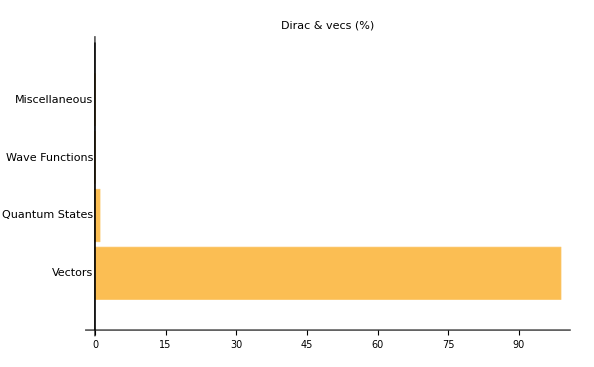

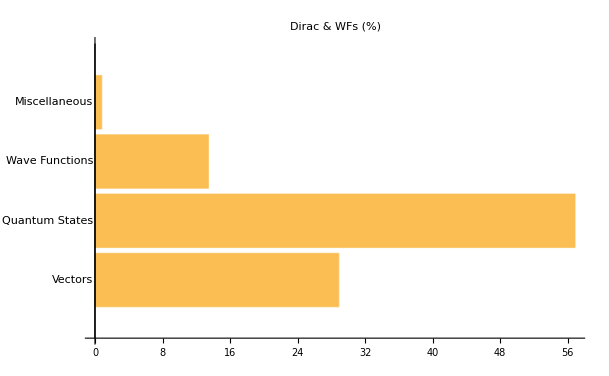

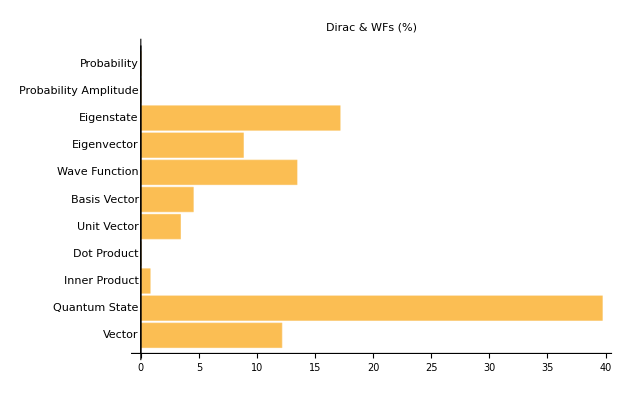

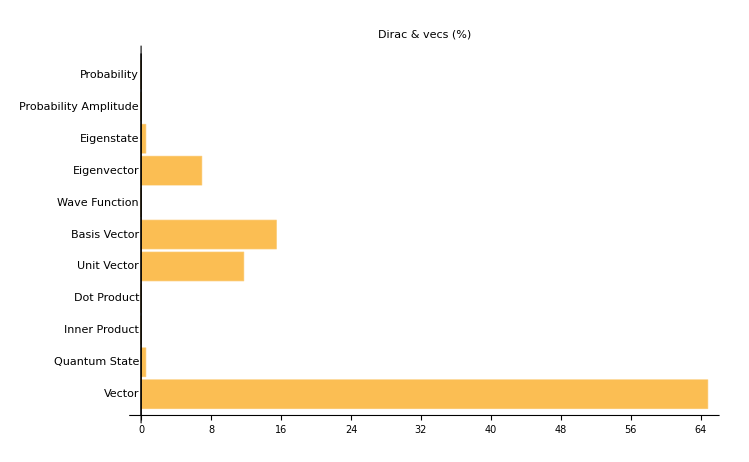

```mathematica
(* 
vennArray[[i,j,k,l]];
i = student;
j = concept;
k = expression 1;
l = expression 2;
*)
(*
verticesNum={Property[1,VertexLabels->OverVector["v"]],
Property[2,VertexLabels->OverHat["j"]],
Property[3,VertexLabels->OverHat["S_z"]],
Property[4,VertexLabels->"f(x)"],
Property[5,VertexLabels->"|ψ⟩"],
Property[6,VertexLabels->"|E_2⟩"],
Property[7,VertexLabels->"⟨E_1|"],
Property[8,VertexLabels->"ψ(x)"],
Property[9,VertexLabels->"ψ^*(x)"],
Property[10,VertexLabels->"φ_3(x)"],
Property[11,VertexLabels->"φ_4^*(x)"],
Property[12,VertexLabels->OverVector["u"]·OverVector["v"]],
Property[13,VertexLabels->"⟨ψ|ψ⟩"],
Property[14,VertexLabels->"⟨E_3|ψ⟩"],
Property[15,VertexLabels->"∫ψ^*ψdx"],
Property[16,VertexLabels->"∫φ_1^*ψdx"],
Property[17,VertexLabels->"|⟨E_4|ψ⟩|^2"],
Property[18,VertexLabels->"|∫ψ^*ψdx|^2"],
Property[19,VertexLabels->"|∫φ_2^*ψdx|^2"],
Property[20,VertexLabels->"⟨ψ|"]};
*)


(* NOTE: THIS IS PROBABLY NOT EXACTLY HOW I WANT TO DO IT, AS IT IS LIKELY DOUBLE-COUNTING SOME OF THE CONCEPTS, AS WE ARE ADDING UNIT VECTOR ON TOP OF BASIS VECTOR ON TOP OF VECTOR, E.G.  I BELIEVE I SOLVED THIS ABOVE WHEN MAKING VENN DIAGRAMS, BUT I'LL NEED TO CHECK/REDO IT DOWN BELOW *)

vennArray[[All,All,1,2]]//MatrixForm;
Total[vennArray[[All,All,1,2]]]//MatrixForm;
Total[vennArray[[All,All,1,8]]]+Total[vennArray[[All,All,1,9]]]+Total[vennArray[[All,All,1,10]]]+Total[vennArray[[All,All,1,11]]];

BarChart[
Total[vennArray[[All,All,1,8]]]+Total[vennArray[[All,All,1,9]]]+Total[vennArray[[All,All,1,10]]]+Total[vennArray[[All,All,1,11]]],
PlotLabel->OverHat["j"]" & WFs",
ChartLabels->labels,
BarOrigin->Left
];

(* Here I add up all of the edges between all WF and Dirac expressions, with "wfDiracConns" returning a list of how many students made that connection per concept *)
wfDiracConns=0;
Do[
Do[
wfDiracConns=wfDiracConns+Total[vennArray[[All,All,i,j]]],
{i,{8,9,10,11}}
],
{j,{5,6,7,20}}
]

(* Here I add up all of the edges between all generic vector and Dirac expressions, with "vecDiracConns" returning a list of how many students made that connection per concept *)
vecDiracConns=0;
Do[
Do[
vecDiracConns=vecDiracConns+Total[vennArray[[All,All,i,j]]],
{i,{1,2}}
],
{j,{5,6,7,20}}
]





(* Here I turn them into percentages *)
vecDiracPerc=vecDiracConns/Total[vecDiracConns]*100;
wfDiracPerc=wfDiracConns/Total[wfDiracConns]*100;


(* 
here I combine similar concepts into overarching concepts;
vector, unit vector, basis vector, eigenvector -> "vector";
quantum state, eigenstate -> "quantum state";
wave function -> "wave functions";
inner product, dot product, probability amplitude, probability -> "miscellaneous"
*)
vecDiracVecsPerc=vecDiracPerc[[1]]+vecDiracPerc[[5]]+vecDiracPerc[[6]]+vecDiracPerc[[8]];
wfDiracVecsPerc=wfDiracPerc[[1]]+wfDiracPerc[[5]]+wfDiracPerc[[6]]+wfDiracPerc[[8]];

vecDiracStatePerc=vecDiracPerc[[2]]+vecDiracPerc[[9]];
wfDiracStatePerc=wfDiracPerc[[2]]+wfDiracPerc[[9]];

vecDiracWFPerc=vecDiracPerc[[7]];
wfDiracWFPerc=wfDiracPerc[[7]];

vecDiracMiscPerc=vecDiracPerc[[3]]+vecDiracPerc[[4]]+vecDiracPerc[[10]]+vecDiracPerc[[11]];
wfDiracMiscPerc=wfDiracPerc[[3]]+wfDiracPerc[[4]]+wfDiracPerc[[10]]+wfDiracPerc[[11]];

agglomLabels={"Vectors","Quantum States","Wave Functions","Miscellaneous"};
vecDiracAgglomPerc={vecDiracVecsPerc,vecDiracStatePerc,vecDiracWFPerc,vecDiracMiscPerc};
wfDiracAgglomPerc={wfDiracVecsPerc,wfDiracStatePerc,wfDiracWFPerc,wfDiracMiscPerc};

N[vecDiracPerc]
N[vecDiracPerc[[1]]]


(* Here I create bar charts *)

BarChart[
vecDiracAgglomPerc,
PlotLabel->"Dirac & vecs (%)",
ChartLabels->agglomLabels,
BarOrigin->Left
]

BarChart[
wfDiracAgglomPerc,
PlotLabel->"Dirac & WFs (%)",
ChartLabels->agglomLabels,
BarOrigin->Left
]


BarChart[
wfDiracConns,
PlotLabel->"Dirac & WFs",
ChartLabels->labels,
BarOrigin->Left
];

BarChart[
vecDiracConns,
PlotLabel->"Dirac & vecs",
ChartLabels->labels,
BarOrigin->Left
];

BarChart[
wfDiracPerc,
PlotLabel->"Dirac & WFs (%)",
ChartLabels->labels,
BarOrigin->Left
]

BarChart[
vecDiracPerc,
PlotLabel->"Dirac & vecs (%)",
ChartLabels->labels,
BarOrigin->Left
]
```

### 1.3 Making bar charts for shared concepts

{1082,16,2,0}

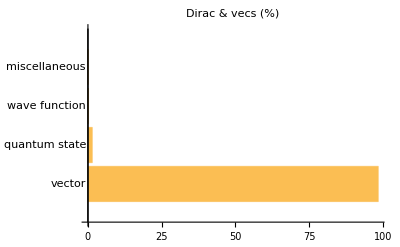

{460,972,322,12}

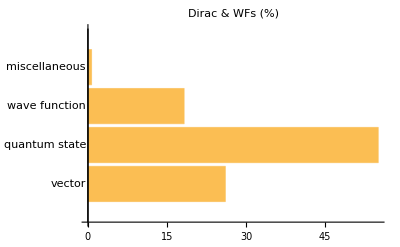

{1892,1520,148,28}

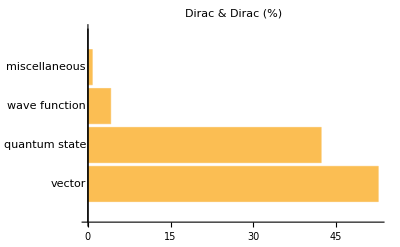

{318,880,1594,124}

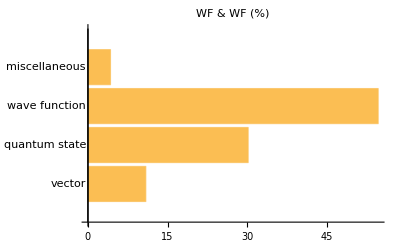

```mathematica
(* 
vennArray[[i,j,k,l]];
i = student;
j = concept;
k = expression 1;
l = expression 2;
*)

(*
CONCEPTS:
vectors: 1, 5, 6, 8
state:   2, 9
WF:      7
misc:  3, 4, 10, 11

(3: inner product,
4: dot product,
10: probability amplitude,
11: probability)
*)

(*
EXPRESSIONS:
generic vector:  1, 2 
Dirac bras/kets: 5, 6, 7, 20 
WFs:             8, 9, 10, 11
*)

(* sums up the various concept types, creating a new array with the following indices:

concarray[[i,j,k,l]];

i = concept type (vector, state, WF, misc.);
j = student;
k = expression 1;
l = expression 2;
*)

(* this is the array for the WF, generic vector, and Dirac expressions *)
concArray=Table[0,4];
concArray[[1]]=vennArray[[All,1,All,All]]+vennArray[[All,5,All,All]]+vennArray[[All,6,All,All]]+vennArray[[All,8,All,All]]; (* vector concepts *)
concArray[[2]]=vennArray[[All,2,All,All]]+vennArray[[All,9,All,All]]; (* quantum state concepts *)
concArray[[3]]=vennArray[[All,7,All,All]]; (* WF concept *)
concArray[[4]]=vennArray[[All,3,All,All]]+vennArray[[All,4,All,All]]+vennArray[[All,10,All,All]]+vennArray[[All,11,All,All]]; (* all other concepts *)

(* here I make the array for looking at the inner product groups (both squares and non-squares) *)
IPconcArray=Table[0,5];
IPconcArray[[1]]=vennArray[[All,3,All,All]]+vennArray[[All,4,All,All]]; (* combines inner product & dot product *)
IPconcArray[[2]]=vennArray[[All,10,All,All]]; (* probability amplitude *)
IPconcArray[[3]]=vennArray[[All,11,All,All]]; (* probability *)
IPconcArray[[4]]=vennArray[[All,7,All,All]]; (* wave function *)
IPconcArray[[5]]=vennArray[[All,1,All,All]]+vennArray[[All,2,All,All]]+vennArray[[All,5,All,All]]+vennArray[[All,6,All,All]]+vennArray[[All,8,All,All]]+vennArray[[All,9,All,All]]; (* combines all other concepts together *)

concArray[[1,1]]//MatrixForm;

(* Here I replace all non-zero elements to one for the concArray, as this will eliminate double-counting concepts of the same type *)
For[i=1,i<=4,i++,
For[j=1,j<=nStu,j++,
For[k=1,k<=nExp,k++,
For[l=1,l<=nExp,l++,
If[concArray[[i,j,k,l]]>0,
concArray[[i,j,k,l]]=1
]
]
]
]
]

(* Here I replace all non-zero elements to one for the IPconcArray, as this will eliminate double-counting concepts of the same type *)
For[i=1,i<=5,i++,
For[j=1,j<=nStu,j++,
For[k=1,k<=nExp,k++,
For[l=1,l<=nExp,l++,
If[IPconcArray[[i,j,k,l]]>0,
IPconcArray[[i,j,k,l]]=1
]
]
]
]
]

concArray[[1,1]]//MatrixForm;

(* adds up to get the number of students who used each pair of expressions at least once for each concept type:

stuSumConcArray[[i,j,k]];

i = concept type;
j = expression 1;
k = expression 2;
*)
stuSumConcArray=Table[0,4];
For[i=1,i<=4,i++,
For[j=1,j<=nStu,j++,
stuSumConcArray[[i]]=stuSumConcArray[[i]]+concArray[[i,j]]
]
]

IPstuSumConcArray=Table[0,5];
For[i=1,i<=5,i++,
For[j=1,j<=nStu,j++,
IPstuSumConcArray[[i]]=IPstuSumConcArray[[i]]+IPconcArray[[i,j]]
]
]

stuSumConcArray[[1,1,5]];
stuSumConcArray[[1]]//MatrixForm;

(* here we fill out the table of tables:

finalArray[[i,j,k]];

i = concept type        (vector, state, WF, misc.);
j = expression type 1   (generic vector, bras & kets, WFs);
k = expression type 2   (generic vector, bras & kets, WFs);
*)
finalArray=Table[0,4,3,3];
For[i=1,i<=4,i++,

Do[
Do[
finalArray[[i,1,2]]=finalArray[[i,1,2]]+stuSumConcArray[[i,j,k]],
{j,{1,2}}
],
{k,{5,6,7,20}}
];

Do[
Do[
finalArray[[i,1,3]]=finalArray[[i,1,3]]+stuSumConcArray[[i,j,k]],
{j,{1,2}}
],
{k,{8,9,10,11}}
];

Do[
Do[
finalArray[[i,2,3]]=finalArray[[i,2,3]]+stuSumConcArray[[i,j,k]],
{j,{5,6,7,20}}
],
{k,{8,9,10,11}}
];

Do[
Do[
finalArray[[i,2,2]]=finalArray[[i,2,2]]+stuSumConcArray[[i,j,k]],
{j,{5,6,7,20}}
],
{k,{5,6,7,20}}
];

Do[
Do[
finalArray[[i,3,3]]=finalArray[[i,3,3]]+stuSumConcArray[[i,j,k]],
{j,{8,9,10,11}}
],
{k,{8,9,10,11}}
]

];

(* here we fill out the table of tables:

IPfinalArray[[i,j,k]];

i = concept type        (inner/dot product, prob ampl, prob, wf, misc.);
j = expression type 1   (genDP, DIP, IPI, DIP2, IPI2);
k = expression type 2   (genDP, DIP, IPI, DIP2, IPI2);
*)
IPfinalArray=Table[0,5,5,5];
For[i=1,i<=5,i++,

Do[
Do[
IPfinalArray[[i,1,2]]=IPfinalArray[[i,1,2]]+IPstuSumConcArray[[i,j,k]],
{j,{12}}
],
{k,{13,14}}
];

Do[
Do[
IPfinalArray[[i,1,3]]=IPfinalArray[[i,1,3]]+IPstuSumConcArray[[i,j,k]],
{j,{12}}
],
{k,{15,16}}
];

Do[
Do[
IPfinalArray[[i,1,4]]=IPfinalArray[[i,1,4]]+IPstuSumConcArray[[i,j,k]],
{j,{12}}
],
{k,{17}}
];

Do[
Do[
IPfinalArray[[i,1,5]]=IPfinalArray[[i,1,5]]+IPstuSumConcArray[[i,j,k]],
{j,{12}}
],
{k,{18,19}}
];

Do[
Do[
IPfinalArray[[i,2,3]]=IPfinalArray[[i,2,3]]+IPstuSumConcArray[[i,j,k]],
{j,{13,14}}
],
{k,{15,16}}
];

Do[
Do[
IPfinalArray[[i,2,4]]=IPfinalArray[[i,2,4]]+IPstuSumConcArray[[i,j,k]],
{j,{13,14}}
],
{k,{17}}
];

Do[
Do[
IPfinalArray[[i,2,5]]=IPfinalArray[[i,2,5]]+IPstuSumConcArray[[i,j,k]],
{j,{13,14}}
],
{k,{18,19}}
];

Do[
Do[
IPfinalArray[[i,3,4]]=IPfinalArray[[i,3,4]]+IPstuSumConcArray[[i,j,k]],
{j,{15,16}}
],
{k,{17}}
];

Do[
Do[
IPfinalArray[[i,3,5]]=IPfinalArray[[i,3,5]]+IPstuSumConcArray[[i,j,k]],
{j,{15,16}}
],
{k,{18,19}}
];

Do[
Do[
IPfinalArray[[i,4,5]]=IPfinalArray[[i,4,5]]+IPstuSumConcArray[[i,j,k]],
{j,{17}}
],
{k,{18,19}}
];

];

finalArray[[All,1,2]];


finalArray[[All,1,2]];
finalArray[[1]];
Flatten[finalArray[[1]]];

(* finalArray[[i,j,k]];

i = concept type        (vector, state, WF, misc.);
j = expression type 1   (generic vector, bras & kets, WFs);
k = expression type 2   (generic vector, bras & kets, WFs);
*)

labels={"vector","quantum state","wave function","miscellaneous"};
IPlabels={"inner/dot product","probability amplitude","probability","wave function","miscellaneous"};


(* here are all of the bar charts for the generic vector, WF, and Dirac expression subgroups *)
N[finalArray[[All,1,2]]/Total[finalArray[[All,1,2]]]*100];
finalArray[[All,1,2]]

BarChart[
finalArray[[All,1,2]]/Total[finalArray[[All,1,2]]]*100,
PlotLabel->"Dirac & vecs (%)",
ChartLabels->labels,
BarOrigin->Left
]


N[finalArray[[All,2,3]]/Total[finalArray[[All,2,3]]]*100];
finalArray[[All,2,3]]

BarChart[
finalArray[[All,2,3]]/Total[finalArray[[All,2,3]]]*100,
PlotLabel->"Dirac & WFs (%)",
ChartLabels->labels,
BarOrigin->Left
]


N[finalArray[[All,2,2]]/Total[finalArray[[All,2,2]]]*100];
finalArray[[All,2,2]]

BarChart[
finalArray[[All,2,2]]/Total[finalArray[[All,2,2]]]*100,
PlotLabel->"Dirac & Dirac (%)",
ChartLabels->labels,
BarOrigin->Left
]


N[finalArray[[All,3,3]]/Total[finalArray[[All,3,3]]]*100];
finalArray[[All,3,3]]

BarChart[
finalArray[[All,3,3]]/Total[finalArray[[All,3,3]]]*100,
PlotLabel->"WF & WF (%)",
ChartLabels->labels,
BarOrigin->Left
]


(*
N[finalArray[[All,1,3]]/Total[finalArray[[All,1,3]]]*100];
finalArray[[All,1,3]]

BarChart[
finalArray[[All,1,3]]/Total[finalArray[[All,1,3]]]*100,
PlotLabel->"vecs & WFs (%)",
ChartLabels->labels,
BarOrigin->Left
]


BarChart[
finalArray[[All,1,2]],
PlotLabel->"Dirac & vecs",
ChartLabels->labels,
BarOrigin->Left
]


BarChart[
finalArray[[All,2,3]],
PlotLabel->"Dirac & WFs",
ChartLabels->labels,
BarOrigin->Left
]


BarChart[
finalArray[[All,1,3]],
PlotLabel->"vecs & WFs",
ChartLabels->labels,
BarOrigin->Left
]




(*
IPfinalArray[[i,j,k]];

i = concept type        (inner/dot product, prob ampl, prob, misc.);
j = expression type 1   (genDP, DIP, IPI, DIP2, IPI2);
k = expression type 2   (genDP, DIP, IPI, DIP2, IPI2);
*)

(* here I generate a bunch of bar charts showing conceptual breakdown of connections between subsets of IP and IP2 expressions *)

(*
IPfinalArray[[All,1,2]]
BarChart[
IPfinalArray[[All,1,2]]/Total[IPfinalArray[[All,1,2]]]*100,
PlotLabel->"genDP & DIP (%)",
ChartLabels->IPlabels,
BarOrigin->Left
]

IPfinalArray[[All,1,3]]
BarChart[
IPfinalArray[[All,1,3]]/Total[IPfinalArray[[All,1,3]]]*100,
PlotLabel->"genDP & IPI (%)",
ChartLabels->IPlabels,
BarOrigin->Left
]
*)

IPfinalArray[[All,1,4]]
BarChart[
IPfinalArray[[All,1,4]]/Total[IPfinalArray[[All,1,4]]]*100,
PlotLabel->"genDP & DIP2 (%)",
ChartLabels->IPlabels,
BarOrigin->Left
];

IPfinalArray[[All,1,5]]
BarChart[
IPfinalArray[[All,1,5]]/Total[IPfinalArray[[All,1,5]]]*100,
PlotLabel->"genDP & IPI2 (%)",
ChartLabels->IPlabels,
BarOrigin->Left
];

(*
IPfinalArray[[All,2,3]]
BarChart[
IPfinalArray[[All,2,3]]/Total[IPfinalArray[[All,2,3]]]*100,
PlotLabel->"DIP & IPI (%)",
ChartLabels->IPlabels,
BarOrigin->Left
]
*)

IPfinalArray[[All,2,4]]
BarChart[
IPfinalArray[[All,2,4]]/Total[IPfinalArray[[All,2,4]]]*100,
PlotLabel->"DIP & DIP2 (%)",
ChartLabels->IPlabels,
BarOrigin->Left
];

IPfinalArray[[All,2,5]]
BarChart[
IPfinalArray[[All,2,5]]/Total[IPfinalArray[[All,2,5]]]*100,
PlotLabel->"DIP & IPI2 (%)",
ChartLabels->IPlabels,
BarOrigin->Left
];

IPfinalArray[[All,3,4]]
BarChart[
IPfinalArray[[All,3,4]]/Total[IPfinalArray[[All,3,4]]]*100,
PlotLabel->"IPI & DIP2 (%)",
ChartLabels->IPlabels,
BarOrigin->Left
];

IPfinalArray[[All,3,5]]
BarChart[
IPfinalArray[[All,3,5]]/Total[IPfinalArray[[All,3,5]]]*100,
PlotLabel->"IPI & IPI2 (%)",
ChartLabels->IPlabels,
BarOrigin->Left
];

(*
IPfinalArray[[All,4,5]]
BarChart[
IPfinalArray[[All,4,5]]/Total[IPfinalArray[[All,4,5]]]*100,
PlotLabel->"DIP2 & IPI2 (%)",
ChartLabels->IPlabels,
BarOrigin->Left
]
*)
```

```mathematica
Dimensions[concArray]
concArray[[1,1]]//MatrixForm
```

{4,139,20,20}

(0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Dimensions[IPstuSumConcArray]
Dimensions[IPconcArray]
```

### 1.3.1 Counting # connections/concept type for different expression type pairs (turns out this was already happening)

{{{5,6,7,20},{8,9,10,11}},{{5,6,7,20},{5,6,7,20}},{{8,9,10,11},{8,9,10,11}}}

{{5,6,7,20},{8,9,10,11}}

{5,6,7,20}

3

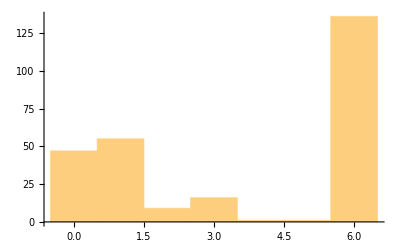

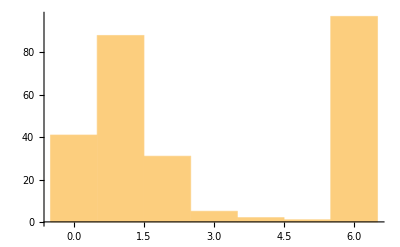

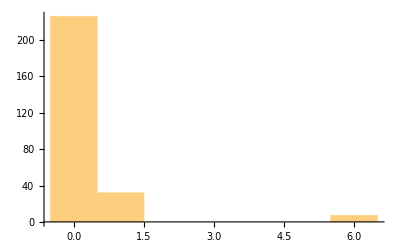

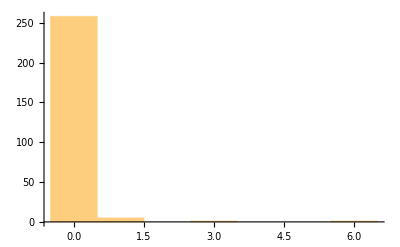

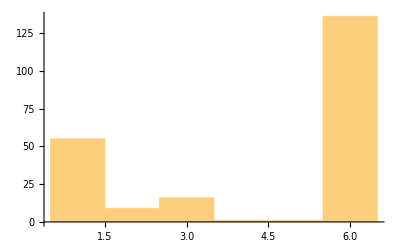

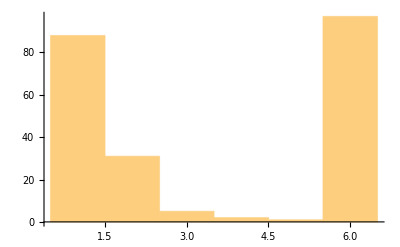

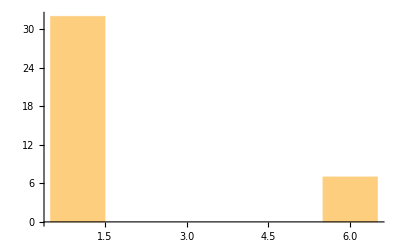

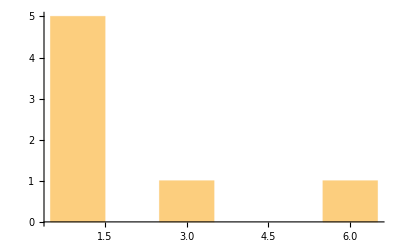

```mathematica
(* 
vennArray[[i,j,k,l]];
i = student;
j = concept;
k = expression 1;
l = expression 2;
*)


(* the next chunk will sum up the various concept types (WHILE ONLY COUNTING THE FIRST INSTANCE OF A GIVEN CONSEPT TYPE PER STUDENT), creating a new array with the following indices:

concarray[[i,j,k,l]];

i = concept type (vector, state, WF, misc.);
j = student;
k = expression 1;
l = expression 2;
*)

(*
CONCEPTS:
vectors: 1, 5, 6, 8
state:   2, 9
WF:      7
misc:  3, 4, 10, 11

(3: inner product,
4: dot product,
10: probability amplitude,
11: probability)
*)

(*
EXPRESSIONS:
generic vector:  1, 2 
Dirac bras/kets: 5, 6, 7, 20 
WFs:             8, 9, 10, 11
*)

(* this is the array for the WF, generic vector, and Dirac expressions *)

concArray[[1,1]]//MatrixForm;

Total[concArray[[1]]]//MatrixForm;
Drop[Total[concArray[[1]]],10]//MatrixForm;

Delete[Total[concArray[[1]]],{{1},{3},{5}}]//MatrixForm;

nStu;
Max[Total[concArray[[1]]]];

Delete[
Transpose[Delete[
Total[concArray[[1]]],{{1},{2},{3},{4},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19}}
]],{{1},{2},{3},{4},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19}}
]//MatrixForm;

(*concarray[[i,j,k,l]];

i = concept type (vector, state, WF, misc.);
j = student;
k = expression 1;
l = expression 2;
*)

(* here I define the list that will store the count of each concept type's number of connections between a given subgroup of expressions for each student

spinsStudCounts=[[i,j]]
i = expression type pair (1: Dirac-WF, 2: Dirac-Dirac, 3: WF-WF)
j = concept type (1: vector, 2: quantum state, 3: WF, 4: misc.)
k = student

 *)
spinsStudCounts=Table[0,3,4,nStu];

concepts={{1,5,6,8},{2,9},{7},{3,4,10,11}};
expressions={{5,6,7,20},{8,9,10,11}};
expressionPairs={{expressions[[1]],expressions[[2]]},{expressions[[1]],expressions[[1]]},{expressions[[2]],expressions[[2]]}};

expressionPairs
expressionPairs[[1]]
expressionPairs[[1,1]]

Length@expressionPairs


For[i=1,i<=Length@expressionPairs,i++,
For[j=1,j<=Length@concepts,j++,
For[m=1,m<=Length@expressionPairs[[i,1]],m++,
For[n=1,n<=Length@expressionPairs[[i,2]],n++,
If[m>n,
For[k=1,k<=nStu,k++,
spinsStudCounts[[i,j,k]]=spinsStudCounts[[i,j,k]]+concArray[[j,k,expressionPairs[[i,1,m]],expressionPairs[[i,2,n]]]]
]
]
]
]
]
]


spinsStudCounts[[1,2]]==spinsStudCounts[[2,2]];

DistributionChart[spinsStudCounts[[2,1]]];
DistributionChart[spinsStudCounts[[2,2]]];

Histogram[spinsStudCounts[[2,1]]]
Histogram[spinsStudCounts[[2,2]]]
Histogram[spinsStudCounts[[2,3]]]
Histogram[spinsStudCounts[[2,4]]]

Histogram[spinsStudCounts[[2,1]],{0.5,6.5,1}]
Histogram[spinsStudCounts[[2,2]],{0.5,6.5,1}]
Histogram[spinsStudCounts[[2,3]],{0.5,6.5,1}]
Histogram[spinsStudCounts[[2,4]],{0.5,6.5,1}]
```

{139,11,20,20}

{11,20,20}

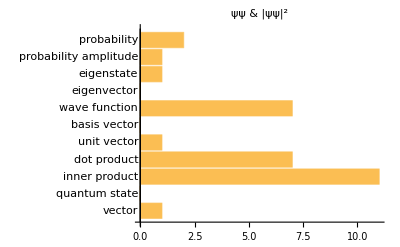

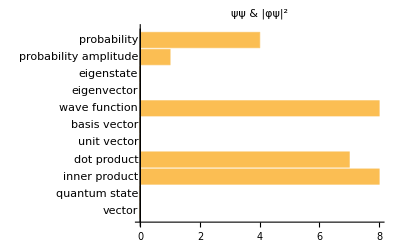

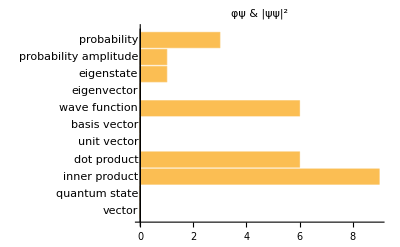

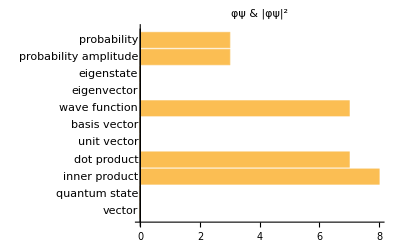

```mathematica
Dimensions[vennArray]
Dimensions[Total[vennArray]]

concList={"vector","quantum state","inner product","dot product","unit vector","basis vector","wave function","eigenvector","eigenstate","probability amplitude","probability"};

BarChart[
Total[vennArray][[All,15,18]],
PlotLabel->"ψψ & |ψψ|^2",
ChartLabels->concList,
BarOrigin->Left
]

BarChart[
Total[vennArray][[All,15,19]],
PlotLabel->"ψψ & |φψ|^2",
ChartLabels->concList,
BarOrigin->Left
]
BarChart[
Total[vennArray][[All,16,18]],
PlotLabel->"φψ & |ψψ|^2",
ChartLabels->concList,
BarOrigin->Left
]
BarChart[
Total[vennArray][[All,16,19]],
PlotLabel->"φψ & |φψ|^2",
ChartLabels->concList,
BarOrigin->Left
]

Total[vennArray][[All,15,18]];
Total[vennArray][[All,15,19]];
Total[vennArray][[All,16,18]];
Total[vennArray][[All,16,19]];
```

### 1.3.2 individual expressions per concept

{0.969811,0.701887,0.177358,0.0377358,0.573585,0.524528,0.464151,0.10566,0.0792453,0.090566,0.0754717,0.196226,0.0264151,0.0301887,0.00754717,0.,0.00377358,0.00377358,0.,0.467925}

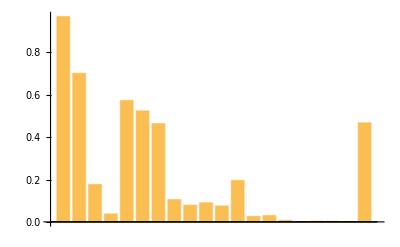

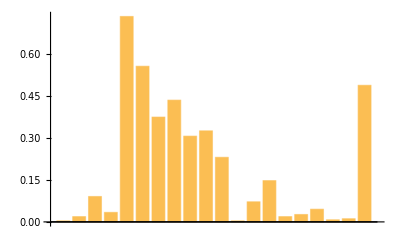
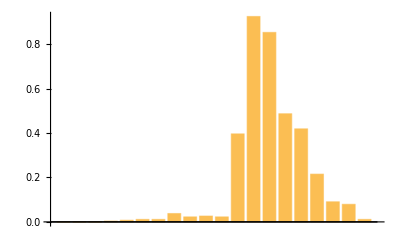
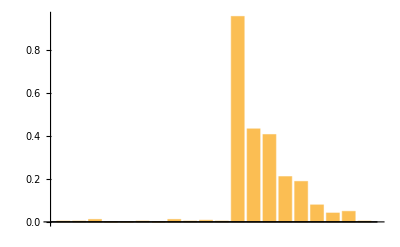
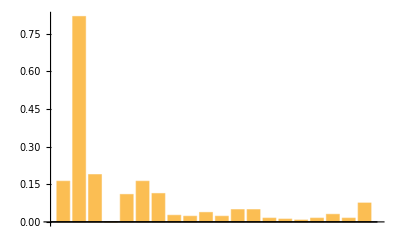
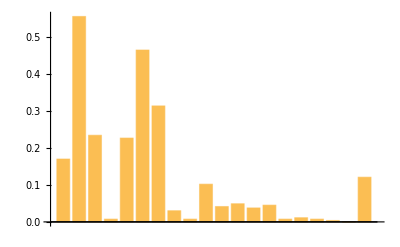
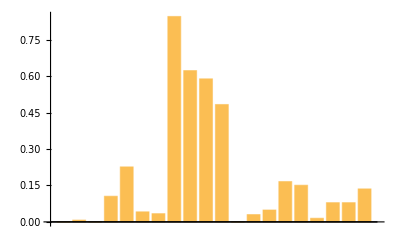
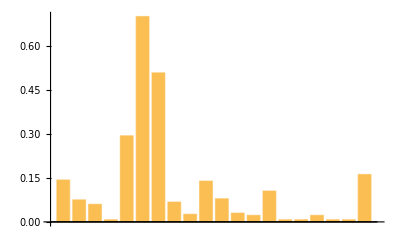
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Dimensions[data];

data[[1]];
data[[1,1]];

Length@data[[1,1]];

(*

data[[i,j,k]]

i: student
j: concept
k: expression (length of j list is limited by the number of expressions students chose for the jth concept, so the number of k expressions varies for every i,j)

*)

indivExpPerConc=Table[0,nConc,nExp];
(* 
indivExpPerConc[[i,j]]
i: concept
j: expression
*)

(* initializes the table that will maintain the normalized values (the fraction of students that used a given expression for a given concept) *)
indivExpPerConcNormed=Table[0,nConc,nExp];



For[i=1,i<=nStu,i++,
For[j=1,j<=nConc,j++,
If[data[[i,j]]!={26}, (* this makes it so it skips past every time a student didn't drag any expression in, as those were coded "z", which was changed to 26 here *)
For[k=1,k<=Length@data[[i,j]],k++,
(* iterates the concept's expression count by one for every time a student used an expression for a given concept *)
indivExpPerConc[[j,data[[i,j,k]]]]++
]
];
indivExpPerConcNormed[[j]]=N[indivExpPerConc[[j]]/nStu]
]
]


indivExpPerConc[[1]];
indivExpPerConcNormed[[1]]

Export["F21+F22SpinsIndivExpPerConc.xlsx",indivExpPerConc];
Export["F21+F22SpinsIndivExpPerConcNormed.xlsx",indivExpPerConcNormed];


spinIndivNormedCharts=Table[0,nConc];

BarChart[indivExpPerConcNormed[[1]]]


For[i=1,i<=nConc,i++,
spinIndivNormedCharts[[i]]=BarChart[indivExpPerConcNormed[[i]]]
]

spinIndivNormedCharts
```

### 1.4 Inter-community concepts

{11,20,20}

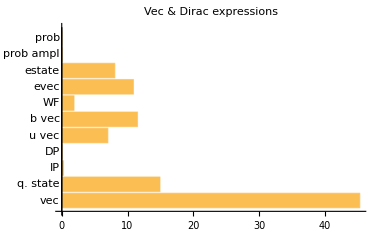

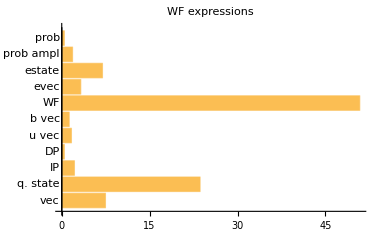

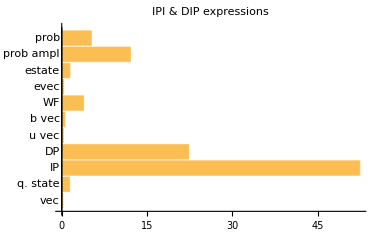

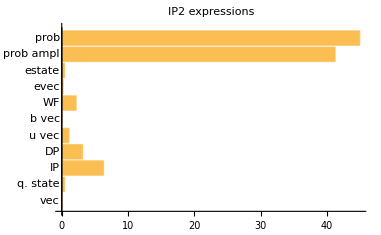

```mathematica
Dimensions[pieArray]

(* pieArray[[i,j,k]]
i: concept
j: expression
k: expression
*)

(*
Concepts
1: vector
2: quantum state
3: inner product
4: dot product
5: unit vector
6: basis vector
7: wave function
8: eigenvector
9: eigenstate
10: probability amplitude
11: probability
*)
concList={"vec","q. state","IP","DP","u vec","b vec","WF","evec","estate","prob ampl","prob"};
(*
Expressions
1: v
2: j
3: Sz
4: f(x)
5: ψ ket
6: E ket
7: E bra
8: ψ(x)
9: ψ*(x)
10: φ(x)
11: φ*(x)
12: u.v
13: ψψ DIP
14: Eψ DIP
15: ψψ IPI
16: φψ IPI
17: Eψ DIP2
18: ψψ IPI2
19: φψ IPI2
20: ψ bra
*)
pieArray[[All,1,2]]//MatrixForm;

spinsComm1={1,2,5,6,7,20};
spinsComm2={8,9,10,11};
spinsComm3={13,14,15,16};
spinsComm4={17,18,19};

spinsComm1Sum=Table[0,nConc];
spinsComm2Sum=Table[0,nConc];
spinsComm3Sum=Table[0,nConc];
spinsComm4Sum=Table[0,nConc];

For[i=1,i<=Length@spinsComm1,i++,
For[j=1,j<=Length@spinsComm1,j++,
If[i<j,
spinsComm1Sum=spinsComm1Sum+pieArray[[All,spinsComm1[[i]],spinsComm1[[j]]]]
]
]
]
For[i=1,i<=Length@spinsComm2,i++,
For[j=1,j<=Length@spinsComm2,j++,
If[i<j,
spinsComm2Sum=spinsComm2Sum+pieArray[[All,spinsComm2[[i]],spinsComm2[[j]]]]
]
]
]
For[i=1,i<=Length@spinsComm3,i++,
For[j=1,j<=Length@spinsComm3,j++,
If[i<j,
spinsComm3Sum=spinsComm3Sum+pieArray[[All,spinsComm3[[i]],spinsComm3[[j]]]]
]
]
]
For[i=1,i<=Length@spinsComm4,i++,
For[j=1,j<=Length@spinsComm4,j++,
If[i<j,
spinsComm4Sum=spinsComm4Sum+pieArray[[All,spinsComm4[[i]],spinsComm4[[j]]]]
]
]
]

spinsComm1Sum//MatrixForm;
spinsComm2Sum//MatrixForm;
spinsComm3Sum//MatrixForm;
spinsComm4Sum//MatrixForm;

BarChart[spinsComm1Sum/Total[spinsComm1Sum]*100,PlotLabel->"Vec & Dirac expressions",ChartLabels->concList,BarOrigin->Left]
BarChart[spinsComm2Sum/Total[spinsComm2Sum]*100,PlotLabel->"WF expressions",ChartLabels->concList,BarOrigin->Left]
BarChart[spinsComm3Sum/Total[spinsComm3Sum]*100,PlotLabel->"IPI & DIP expressions",ChartLabels->concList,BarOrigin->Left]
BarChart[spinsComm4Sum/Total[spinsComm4Sum]*100,PlotLabel->"IP2 expressions",ChartLabels->concList,BarOrigin->Left]
```

## making “quantum state” figure for ch4

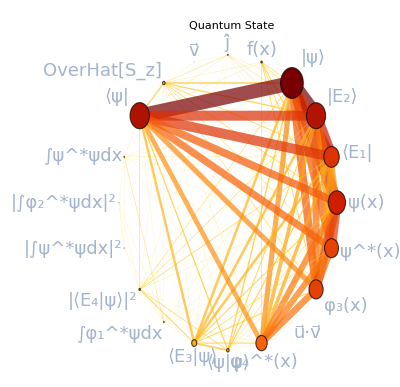

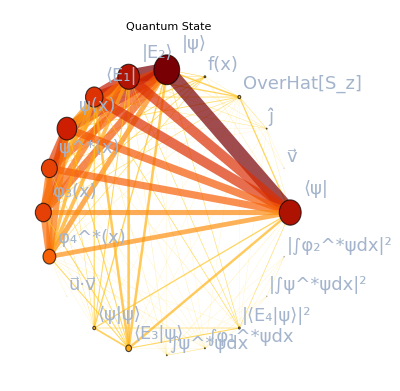

{1,124}

{1,663}

```mathematica
Total[vennArray[[All,2]]]//MatrixForm;

qStateAdj=Total[vennArray[[All,2]]];

qStateAdjNoInf=qStateAdj;

qStateAdj//MatrixForm;

For[i=1,i<=nExp,i++,
For[j=1,j<=nExp,j++,
If[qStateAdj[[i,j]]==0,
qStateAdj[[i,j]]=Infinity
]
]
]

qStateAdj//MatrixForm;

vertexLabels={
OverVector["v"],
OverHat["j"],
OverHat["S_z"],
"f(x)",
"|ψ⟩",
"|E_2⟩",
"⟨E_1|",
"ψ(x)",
"ψ^*(x)",
"φ_3(x)",
"φ_4^*(x)",
OverVector["u"]·OverVector["v"],
"⟨ψ|ψ⟩",
"⟨E_3|ψ⟩",
"∫ψ^*ψdx",
"∫φ_1^*ψdx",
"|⟨E_4|ψ⟩|^2",
"|∫ψ^*ψdx|^2",
"|∫φ_2^*ψdx|^2",
"⟨ψ|"
};


edgeWeights=Map[PropertyValue[{g,#},EdgeWeight]&,EdgeList[g]];
weightDegrees=VertexDegree[AdjacencyGraph[qStateAdjNoInf]];
numList=Table[i,{i,nExp}];
degList=Table[0,nExp];
degList1=Table[0,nExp];


For[i=1,i<=nExp,i++,
degList[[i]]=numList[[i]]->weightDegrees[[i]];
degList1[[i]]=vertexLabels[[i]]->weightDegrees[[i]]/Max[weightDegrees]/1.5
]

degList//MatrixForm;

(*Defining the "circle" function.  This is just for making all of the networks share the same morphology for ease of at-a-glance comparison*)
circle[n_]:=Table[{Cos[2*Pi/n*u],Sin[2*Pi/n*u]},{u,1,n}]


shapeFunc=With[{weight=PropertyValue[{WeightedAdjacencyGraph[vertexLabels,qStateAdj],#2},EdgeWeight]},{AbsoluteThickness[weight/12],Line@#1}]&;

(*
WeightedAdjacencyGraph[vertexLabels,qStateAdj,VertexLabels->Automatic,GraphLayout->"CircularEmbedding",EdgeShapeFunction->shapeFunc];

WeightedAdjacencyGraph[vertexLabels,qStateAdj,VertexLabels->Automatic,GraphLayout->"CircularEmbedding",EdgeShapeFunction->shapeFunc,VertexSize->weightDegrees/Max[weightDegrees]];
*)
g=WeightedAdjacencyGraph[vertexLabels,qStateAdj,
VertexLabels->Automatic,
GraphLayout->"CircularEmbedding",
VertexSize->degList1,
VertexLabelStyle->20];

WeightedAdjacencyGraph[vertexLabels,qStateAdj,
VertexLabels->Automatic,
GraphLayout->"CircularEmbedding",
VertexSize->degList1,
VertexLabelStyle->18,
EdgeStyle->Thread[EdgeList[g]->(Directive[Thickness[.005],ColorData[{"SolarColors","Reverse"}][#]]&/@Rescale[edgeWeights])],
PlotLabel->"Quantum State",
LabelStyle->20,
EdgeShapeFunction->shapeFunc,
VertexStyle->Thread[VertexList[g]->(ColorData[{"SolarColors","Reverse"}]/@Rescale[weightDegrees])]
]

WeightedAdjacencyGraph[vertexLabels,qStateAdj,
VertexLabels->Automatic,
VertexCoordinates->circle[nExp],
VertexSize->degList1,
VertexLabelStyle->18,
EdgeStyle->Thread[EdgeList[g]->(Directive[Thickness[.005],ColorData[{"SolarColors","Reverse"}][#]]&/@Rescale[edgeWeights])],
PlotLabel->"Quantum State",
LabelStyle->20,
EdgeShapeFunction->shapeFunc,
VertexStyle->Thread[VertexList[g]->(ColorData[{"SolarColors","Reverse"}]/@Rescale[weightDegrees])]
]

Dimensions[vennArray];

VertexDegree[WeightedAdjacencyGraph[qStateAdj]];

weightDegrees=VertexDegree[AdjacencyGraph[qStateAdjNoInf]];

ColorData["SolarColors"][0];

MinMax[edgeWeights]
MinMax[weightDegrees]

BarLegend[
{{"SolarColors","Reverse"},MinMax[edgeWeights]},
LegendLabel->"edge\nweight",
LabelStyle->16
]

BarLegend[
{{"SolarColors","Reverse"},MinMax[weightDegrees]},
LegendLabel->"vertex\ndegree",
LabelStyle->16
]
```

## making “vector” figure for ch4

```mathematica
Total[vennArray[[All,1]]]//MatrixForm;

vecAdj=Total[vennArray[[All,1]]];

vecAdjNoInf=vecAdj;

For[i=1,i<=nExp,i++,
For[j=1,j<=nExp,j++,
If[vecAdj[[i,j]]==0,
vecAdj[[i,j]]=Infinity
]
]
]


vertexLabels={
OverVector["v"],
OverHat["j"],
OverHat["S_z"],
"f(x)",
"|ψ⟩",
"|E_2⟩",
"⟨E_1|",
"ψ(x)",
"ψ^*(x)",
"φ_3(x)",
"φ_4^*(x)",
OverVector["u"]·OverVector["v"],
"⟨ψ|ψ⟩",
"⟨E_3|ψ⟩",
"∫ψ^*ψdx",
"∫φ_1^*ψdx",
"|⟨E_4|ψ⟩|^2",
"|∫ψ^*ψdx|^2",
"|∫φ_2^*ψdx|^2",
"⟨ψ|"
};

numList=Table[i,{i,nExp}];
degList=Table[0,nExp];
degList1=Table[0,nExp];

weightDegrees=VertexDegree[AdjacencyGraph[vecAdjNoInf]];

For[i=1,i<=nExp,i++,
degList[[i]]=numList[[i]]->weightDegrees[[i]];
degList1[[i]]=vertexLabels[[i]]->weightDegrees[[i]]/Max[weightDegrees]/1.5
]

g=WeightedAdjacencyGraph[vertexLabels,vecAdj,
VertexLabels->Automatic,
GraphLayout->"CircularEmbedding",
VertexSize->degList1,
VertexLabelStyle->20];

edgeWeights=Map[PropertyValue[{g,#},EdgeWeight]&,EdgeList[g]];
weightDegrees=VertexDegree[AdjacencyGraph[vecAdjNoInf]];


(*Defining the "circle" function.  This is just for making all of the networks share the same morphology for ease of at-a-glance comparison*)
circle[n_]:=Table[{Cos[2*Pi/n*u],Sin[2*Pi/n*u]},{u,1,n}]


shapeFunc=With[{weight=PropertyValue[{WeightedAdjacencyGraph[vertexLabels,vecAdj],#2},EdgeWeight]},{AbsoluteThickness[weight/12],Line@#1}]&;

(*
WeightedAdjacencyGraph[vertexLabels,qStateAdj,VertexLabels->Automatic,GraphLayout->"CircularEmbedding",EdgeShapeFunction->shapeFunc];

WeightedAdjacencyGraph[vertexLabels,qStateAdj,VertexLabels->Automatic,GraphLayout->"CircularEmbedding",EdgeShapeFunction->shapeFunc,VertexSize->weightDegrees/Max[weightDegrees]];
*)


WeightedAdjacencyGraph[vertexLabels,vecAdj,
VertexLabels->Automatic,
GraphLayout->"CircularEmbedding",
VertexSize->degList1,
VertexLabelStyle->18,
EdgeStyle->Thread[EdgeList[g]->(Directive[Thickness[.005],ColorData[{"SolarColors","Reverse"}][#]]&/@Rescale[edgeWeights])],
PlotLabel->"Vector",
LabelStyle->20,
EdgeShapeFunction->shapeFunc,
VertexStyle->Thread[VertexList[g]->(ColorData[{"SolarColors","Reverse"}]/@Rescale[weightDegrees])]
]

WeightedAdjacencyGraph[vertexLabels,vecAdj,
VertexLabels->Automatic,
VertexCoordinates->circle[nExp],
VertexSize->degList1,
VertexLabelStyle->18,
EdgeStyle->Thread[EdgeList[g]->(Directive[Thickness[.005],ColorData[{"SolarColors","Reverse"}][#]]&/@Rescale[edgeWeights])],
PlotLabel->"Vector",
LabelStyle->20,
EdgeShapeFunction->shapeFunc,
VertexStyle->Thread[VertexList[g]->(ColorData[{"SolarColors","Reverse"}]/@Rescale[weightDegrees])]
]

Dimensions[vennArray];

VertexDegree[WeightedAdjacencyGraph[qStateAdj]];

ColorData["SolarColors"][0];

MinMax[edgeWeights]
MinMax[weightDegrees]

BarLegend[
{{"SolarColors","Reverse"},MinMax[edgeWeights]},
LegendLabel->"edge\nweight",
LabelStyle->16
]

BarLegend[
{{"SolarColors","Reverse"},MinMax[weightDegrees]},
LegendLabel->"vertex\ndegree",
LabelStyle->16
]
```

-Graphics-

-Graphics-

{1,182}

{0,924}

## making “wave function” figure for ch4

```mathematica
Total[vennArray[[All,7]]]//MatrixForm;

wfAdj=Total[vennArray[[All,7]]];

wfAdjNoInf=wfAdj;

For[i=1,i<=nExp,i++,
For[j=1,j<=nExp,j++,
If[wfAdj[[i,j]]==0,
wfAdj[[i,j]]=Infinity
]
]
]


vertexLabels={
OverVector["v"],
OverHat["j"],
OverHat["S_z"],
"f(x)",
"|ψ⟩",
"|E_2⟩",
"⟨E_1|",
"ψ(x)",
"ψ^*(x)",
"φ_3(x)",
"φ_4^*(x)",
OverVector["u"]·OverVector["v"],
"⟨ψ|ψ⟩",
"⟨E_3|ψ⟩",
"∫ψ^*ψdx",
"∫φ_1^*ψdx",
"|⟨E_4|ψ⟩|^2",
"|∫ψ^*ψdx|^2",
"|∫φ_2^*ψdx|^2",
"⟨ψ|"
};

numList=Table[i,{i,nExp}];
degList=Table[0,nExp];
degList1=Table[0,nExp];

weightDegrees=VertexDegree[AdjacencyGraph[wfAdjNoInf]];

For[i=1,i<=nExp,i++,
degList[[i]]=numList[[i]]->weightDegrees[[i]];
degList1[[i]]=vertexLabels[[i]]->weightDegrees[[i]]/Max[weightDegrees]/1.5
]

g=WeightedAdjacencyGraph[vertexLabels,wfAdj,
VertexLabels->Automatic,
GraphLayout->"CircularEmbedding",
VertexSize->degList1,
VertexLabelStyle->20];

edgeWeights=Map[PropertyValue[{g,#},EdgeWeight]&,EdgeList[g]];
weightDegrees=VertexDegree[AdjacencyGraph[wfAdjNoInf]];


(*Defining the "circle" function.  This is just for making all of the networks share the same morphology for ease of at-a-glance comparison*)
circle[n_]:=Table[{Cos[2*Pi/n*u],Sin[2*Pi/n*u]},{u,1,n}]


shapeFunc=With[{weight=PropertyValue[{WeightedAdjacencyGraph[vertexLabels,wfAdj],#2},EdgeWeight]},{AbsoluteThickness[weight/12],Line@#1}]&;

(*
WeightedAdjacencyGraph[vertexLabels,qStateAdj,VertexLabels->Automatic,GraphLayout->"CircularEmbedding",EdgeShapeFunction->shapeFunc];

WeightedAdjacencyGraph[vertexLabels,qStateAdj,VertexLabels->Automatic,GraphLayout->"CircularEmbedding",EdgeShapeFunction->shapeFunc,VertexSize->weightDegrees/Max[weightDegrees]];
*)


WeightedAdjacencyGraph[vertexLabels,wfAdj,
VertexLabels->Automatic,
GraphLayout->"CircularEmbedding",
VertexSize->degList1,
VertexLabelStyle->18,
EdgeStyle->Thread[EdgeList[g]->(Directive[Thickness[.005],ColorData[{"SolarColors","Reverse"}][#]]&/@Rescale[edgeWeights])],
PlotLabel->"Wave Function",
LabelStyle->20,
EdgeShapeFunction->shapeFunc,
VertexStyle->Thread[VertexList[g]->(ColorData[{"SolarColors","Reverse"}]/@Rescale[weightDegrees])]
]

WeightedAdjacencyGraph[vertexLabels,wfAdj,
VertexLabels->Automatic,
VertexCoordinates->circle[nExp],
VertexSize->degList1,
VertexLabelStyle->18,
EdgeStyle->Thread[EdgeList[g]->(Directive[Thickness[.005],ColorData[{"SolarColors","Reverse"}][#]]&/@Rescale[edgeWeights])],
PlotLabel->"Wave Function",
LabelStyle->20,
EdgeShapeFunction->shapeFunc,
VertexStyle->Thread[VertexList[g]->(ColorData[{"SolarColors","Reverse"}]/@Rescale[weightDegrees])]
]

Dimensions[vennArray];

VertexDegree[WeightedAdjacencyGraph[wfAdj]];

ColorData["SolarColors"][0];

MinMax[edgeWeights]
MinMax[weightDegrees]

BarLegend[
{{"SolarColors","Reverse"},MinMax[edgeWeights]},
LegendLabel->"edge\nweight",
LabelStyle->16
]

BarLegend[
{{"SolarColors","Reverse"},MinMax[weightDegrees]},
LegendLabel->"vertex\ndegree",
LabelStyle->16
]
```

-Graphics-

-Graphics-

{1,162}

{0,630}